## Seasonal Ricker model - EWS in rnb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal_coe"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-2.5;
bh=-0.0568;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="tmax1000_rw0p4";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/trans_rnb/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/trans_rnb/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/trans_rnb/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/trans_rnb/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/trans_rnb/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

20

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Non-breeding",_,_}][[;;,{3,4}]];
(*seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Total",_,_}][[;;,{3,4}]];*)
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;2]],{"Breeding","Non-breeding"},Spacings->{0,0.2},LabelStyle->10]
```

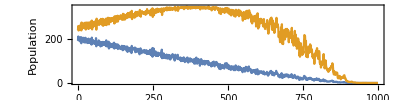

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.2];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

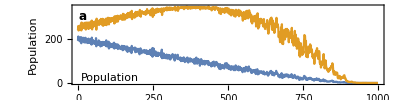

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,All}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Non-breeding growth rate, r_nb"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (single realisations)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

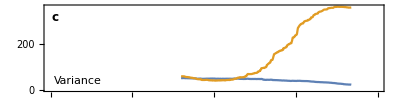

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

```mathematica
ewsVals//Dimensions
```

{2,1000,2}

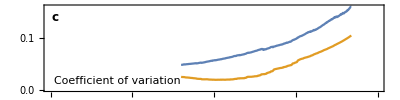

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

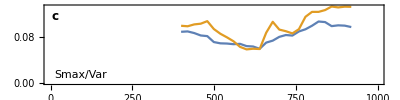

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

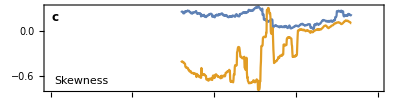

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Kurtosis

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Kurtosis"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

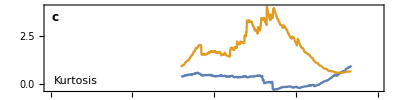

```mathematica
(* Plot EWS *)
plotKurt=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Kurtosis",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

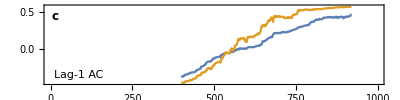

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

### Lag-2 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

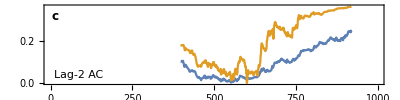

```mathematica
(* Plot EWS *)
plotAc2=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-2 AC",ls],textPos,{-1,0}]}]
```

### Lag-3 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

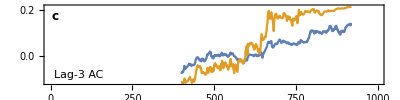

```mathematica
(* Plot EWS *)
plotAc3=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-3 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

14

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.962935 | -0.983478 | -0.968828 | -0.982487 | -0.961118 | -0.932645 | -0.898995 | -0.970811 | -0.959411 | -0.896351 | -0.976043 | -0.94388 | -0.938593 | -0.918656 | -0.962605 | -0.980008 | -0.96602 | -0.948341 | -0.967727 | -0.975052 | -0.883464 | -0.977695 | -0.960898 | -0.936665 | -0.977144 | -0.983368 | -0.958695 | -0.901804 | -0.953132 | -0.94399 | -0.917114 | -0.955225 | -0.955721 | -0.978081 | -0.959135 | -0.976759 | -0.953132 | -0.870962 | -0.980339 | -0.879389 | -0.961559 | -0.822828 | -0.959466 | -0.873055 | -0.964092 | -0.968828 | -0.977915 | -0.937161 | -0.921575 | -0.778549 | -0.987884 | -0.982266 | -0.946799 | -0.867603 | -0.900978 | -0.914801 | -0.972739 | -0.97373 | -0.976924 | -0.975713 | -0.983974 | -0.982817 | -0.969709 | -0.973399 | -0.895415 | -0.980339 | -0.977255 | -0.928129 | -0.972959 | -0.975823 | -0.964698 | -0.960732 | -0.888145 | -0.965193 | -0.903511 | -0.965414 | -0.960567 | -0.931378 | -0.94366 | -0.956437 | -0.974281 | -0.960127 | -0.943274 | -0.861435 | -0.953628 | -0.965964 | -0.975823 | -0.972023 | -0.870852 | -0.741705 | -0.976208 | -0.953573 | -0.940796 | -0.968883 | -0.955721 | -0.905439 | -0.926587 | -0.840837 | -0.820956 | -0.980449
Non-breeding | 0.932975 | 0.97037 | 0.969985 | 0.954674 | 0.97395 | 0.924494 | 0.970425 | 0.97351 | 0.922952 | 0.973895 | 0.972023 | 0.943164 | 0.981385 | 0.986397 | 0.972573 | 0.967947 | 0.94779 | 0.918381 | 0.903731 | 0.922181 | 0.975823 | 0.983974 | 0.974005 | 0.967011 | 0.990032 | 0.970095 | 0.92868 | 0.960072 | 0.963266 | 0.954234 | 0.966956 | 0.946193 | 0.989646 | 0.970756 | 0.977585 | 0.968167 | 0.945752 | 0.976208 | 0.989426 | 0.958585 | 0.924384 | 0.98849 | 0.97764 | 0.909128 | 0.989646 | 0.978631 | 0.958585 | 0.961779 | 0.960237 | 0.937491 | 0.961779 | 0.953518 | 0.927138 | 0.980173 | 0.990748 | 0.963872 | 0.950268 | 0.975272 | 0.976428 | 0.959521 | 0.945697 | 0.969269 | 0.97764 | 0.974391 | 0.949497 | 0.980173 | 0.968002 | 0.991409 | 0.92879 | 0.945422 | 0.985681 | 0.991629 | 0.931543 | 0.968718 | 0.929561 | 0.9403 | 0.949332 | 0.948506 | 0.98122 | 0.951921 | 0.960402 | 0.926256 | 0.968994 | 0.955886 | 0.976098 | 0.978191 | 0.969049 | 0.958034 | 0.993777 | 0.98491 | 0.943605 | 0.970701 | 0.974391 | 0.908357 | 0.975823 | 0.934683 | 0.927743 | 0.979182 | 0.972573 | 0.988269

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.995539 | 0.991078 | 0.99262 | 0.994052 | 0.995814 | 0.994768 | 0.9962 | 0.995869 | 0.996971 | 0.995814 | 0.993722 | 0.992565 | 0.997081 | 0.994878 | 0.994713 | 0.989646 | 0.991629 | 0.995869 | 0.996696 | 0.994327 | 0.994603 | 0.99273 | 0.995154 | 0.994382 | 0.989866 | 0.993336 | 0.994713 | 0.995539 | 0.994823 | 0.993611 | 0.998072 | 0.995264 | 0.997632 | 0.99273 | 0.9924 | 0.989811 | 0.991849 | 0.997356 | 0.99609 | 0.996861 | 0.997356 | 0.996641 | 0.992951 | 0.995925 | 0.995649 | 0.996035 | 0.989646 | 0.991078 | 0.993391 | 0.995154 | 0.98882 | 0.996255 | 0.995319 | 0.9962 | 0.995374 | 0.9962 | 0.992675 | 0.990637 | 0.993887 | 0.992069 | 0.993942 | 0.989922 | 0.995154 | 0.991519 | 0.996585 | 0.99598 | 0.99251 | 0.99631 | 0.994272 | 0.994327 | 0.995098 | 0.988214 | 0.992785 | 0.99284 | 0.995869 | 0.997412 | 0.994327 | 0.99631 | 0.994438 | 0.994713 | 0.994823 | 0.992069 | 0.997191 | 0.994878 | 0.994052 | 0.994933 | 0.99653 | 0.995814 | 0.998788 | 0.996641 | 0.994768 | 0.993116 | 0.989206 | 0.997246 | 0.986948 | 0.995594 | 0.988435 | 0.997356 | 0.995814 | 0.992345
Non-breeding | 0.999835 | 0.999559 | 0.999945 | 1. | 0.999835 | 0.999835 | 0.99989 | 1. | 1. | 0.99989 | 0.99989 | 0.999945 | 1. | 0.99967 | 0.999945 | 0.999725 | 0.999725 | 0.99967 | 0.99989 | 0.999835 | 0.999835 | 0.999945 | 1. | 0.99978 | 1. | 0.99967 | 0.999945 | 0.999945 | 1. | 1. | 0.999835 | 0.99989 | 0.999945 | 0.999504 | 0.999064 | 0.999725 | 0.99967 | 0.999559 | 0.999725 | 0.99989 | 0.99989 | 1. | 1. | 0.99989 | 0.999835 | 0.999945 | 0.99967 | 0.999835 | 0.999449 | 0.99989 | 0.999725 | 1. | 1. | 0.99989 | 1. | 0.999835 | 0.999945 | 0.999504 | 0.999614 | 0.99967 | 0.99989 | 0.999835 | 1. | 0.99978 | 1. | 0.999835 | 0.99978 | 1. | 0.999835 | 0.999559 | 0.999835 | 0.99978 | 1. | 0.999945 | 0.999945 | 1. | 0.999559 | 0.99989 | 0.99978 | 0.999945 | 0.999945 | 0.99967 | 1. | 0.999725 | 1. | 1. | 0.99978 | 1. | 0.999945 | 0.999945 | 1. | 0.999835 | 0.999725 | 1. | 0.99967 | 0.999449 | 0.999725 | 1. | 0.999945 | 0.999835

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.937381 | 0.966846 | 0.971417 | 0.974886 | 0.971968 | 0.934738 | 0.945367 | 0.971527 | 0.980945 | 0.968278 | 0.965469 | 0.975768 | 0.949938 | 0.961614 | 0.956767 | 0.8768 | 0.966846 | 0.946909 | 0.965524 | 0.959631 | 0.964147 | 0.979953 | 0.968553 | 0.975602 | 0.922456 | 0.967176 | 0.937216 | 0.971637 | 0.975327 | 0.973895 | 0.979953 | 0.956051 | 0.944045 | 0.978797 | 0.975768 | 0.983698 | 0.94746 | 0.968002 | 0.973289 | 0.959796 | 0.965138 | 0.965634 | 0.947625 | 0.975547 | 0.968222 | 0.97026 | 0.953353 | 0.943549 | 0.976098 | 0.955115 | 0.973399 | 0.946909 | 0.920363 | 0.953573 | 0.978136 | 0.983368 | 0.964643 | 0.950984 | 0.937546 | 0.972408 | 0.930332 | 0.96613 | 0.956437 | 0.960072 | 0.964643 | 0.972573 | 0.974005 | 0.963156 | 0.944761 | 0.938868 | 0.978907 | 0.943219 | 0.971307 | 0.959245 | 0.968994 | 0.97406 | 0.962495 | 0.920143 | 0.965799 | 0.961724 | 0.959025 | 0.910065 | 0.980063 | 0.975382 | 0.938868 | 0.960512 | 0.960843 | 0.956161 | 0.976428 | 0.979402 | 0.959025 | 0.974556 | 0.979678 | 0.973785 | 0.887209 | 0.972133 | 0.946854 | 0.959411 | 0.967231 | 0.976153
Non-breeding | 0.897563 | 0.975547 | 0.923393 | 0.529891 | 0.902795 | 0.896186 | 0.903346 | 0.914195 | 0.573785 | 0.895746 | 0.970591 | 0.91392 | 0.870742 | 0.942338 | 0.900647 | 0.860443 | 0.842104 | 0.912488 | 0.917775 | 0.894975 | 0.945587 | 0.926311 | 0.944431 | 0.942558 | 0.937546 | 0.956051 | 0.877076 | 0.906485 | 0.956767 | 0.834338 | 0.885557 | 0.774804 | 0.909073 | 0.775685 | 0.949553 | 0.904007 | 0.949332 | 0.891395 | 0.930772 | 0.927633 | 0.880545 | 0.89938 | 0.922732 | 0.922071 | 0.93303 | 0.930001 | 0.954069 | 0.897508 | 0.930442 | 0.945642 | 0.853119 | 0.863693 | 0.944981 | 0.684538 | 0.925651 | 0.949002 | 0.939089 | 0.843536 | 0.952361 | 0.898664 | 0.859727 | 0.889027 | 0.87278 | 0.913479 | 0.894314 | 0.675671 | 0.95539 | 0.752774 | 0.928239 | 0.927688 | 0.888861 | 0.873826 | 0.897949 | 0.943439 | 0.918271 | 0.94041 | 0.904337 | 0.938428 | 0.948231 | 0.725953 | 0.529891 | 0.916949 | 0.902409 | 0.946744 | 0.829382 | 0.836376 | 0.898224 | 0.938923 | 0.893212 | 0.926146 | 0.960953 | 0.909624 | 0.954674 | 0.927138 | 0.891119 | 0.814402 | 0.866226 | 0.952527 | 0.946468 | 0.920253

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-2 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.883905 | 0.914746 | 0.88429 | 0.762798 | 0.929891 | 0.784992 | 0.908468 | 0.89905 | 0.830208 | 0.936831 | 0.800193 | 0.892992 | 0.882418 | 0.827069 | 0.70095 | 0.339777 | 0.882638 | 0.888641 | 0.8654 | 0.833292 | 0.849374 | 0.866942 | 0.920914 | 0.742916 | 0.78681 | 0.920143 | 0.774253 | 0.922952 | 0.860939 | 0.862536 | 0.909459 | 0.920529 | 0.748974 | 0.944431 | 0.380807 | 0.544596 | 0.870907 | 0.890734 | 0.830979 | 0.926532 | 0.87647 | 0.883409 | 0.748258 | 0.8654 | 0.922732 | 0.861104 | 0.898664 | 0.849869 | 0.85824 | 0.883905 | 0.922236 | 0.913865 | 0.907256 | 0.919648 | 0.932645 | 0.850365 | 0.853835 | 0.881371 | 0.824315 | 0.89536 | 0.748258 | 0.870136 | 0.908192 | 0.729919 | 0.933691 | 0.930497 | 0.774088 | 0.759934 | 0.903676 | 0.783781 | 0.76792 | 0.897893 | 0.881481 | 0.367479 | 0.942228 | 0.926697 | 0.741099 | 0.892276 | 0.931213 | 0.380311 | 0.893598 | 0.853449 | 0.8844 | 0.919592 | 0.837643 | 0.877516 | 0.902465 | 0.855266 | 0.925706 | 0.905879 | 0.893432 | 0.803277 | 0.7118 | 0.742916 | 0.777227 | 0.86898 | 0.768415 | 0.95528 | 0.916949 | 0.635688
Non-breeding | 0.830593 | 0.923613 | 0.82795 | 0.574556 | 0.903896 | 0.77607 | 0.767479 | 0.87647 | 0.184745 | 0.89883 | 0.944706 | 0.86182 | 0.746276 | 0.912433 | 0.832907 | 0.676552 | 0.835495 | 0.891505 | 0.892386 | 0.860443 | 0.805204 | 0.525265 | 0.931213 | 0.896351 | 0.895195 | 0.856258 | 0.835605 | 0.83946 | 0.92152 | 0.366543 | 0.841168 | 0.780476 | 0.39061 | 0.747652 | 0.862812 | 0.757345 | 0.92163 | 0.89156 | 0.809115 | 0.916123 | 0.739061 | 0.86898 | 0.837312 | 0.906099 | 0.924549 | 0.854936 | 0.934022 | 0.848603 | 0.784497 | 0.894699 | 0.811152 | 0.854606 | 0.841994 | 0.679141 | 0.899546 | 0.897783 | 0.911717 | 0.785488 | 0.81275 | 0.876305 | 0.747157 | 0.827675 | 0.755693 | 0.914856 | 0.804764 | 0.57015 | 0.939915 | 0.796283 | 0.899325 | 0.919372 | 0.888421 | 0.883134 | 0.821616 | 0.723806 | 0.860278 | 0.930662 | 0.714774 | 0.913204 | 0.914636 | 0.769572 | 0.400799 | 0.850475 | 0.871293 | 0.953077 | 0.727551 | 0.827234 | 0.825472 | 0.879223 | 0.843371 | 0.882638 | 0.89503 | 0.428446 | 0.870907 | 0.867823 | 0.861049 | 0.904062 | 0.917775 | 0.913644 | 0.853835 | 0.828721

```mathematica
(* Box plot *)
boxAc2=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-3 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]]
```

5

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.675065 | 0.718574 | 0.664932 | 0.464794 | 0.890844 | 0.504227 | 0.818092 | 0.805535 | 0.789398 | 0.874157 | 0.449374 | 0.867272 | 0.82806 | 0.946468 | 0.320997 | 0.51023 | 0.729203 | 0.910891 | 0.850695 | 0.810547 | 0.661352 | 0.74969 | 0.710753 | 0.523888 | 0.885006 | -0.0147873 | 0.814071 | 0.918436 | 0.684428 | 0.877461 | 0.814016 | 0.699628 | 0.755858 | 0.896131 | 0.19631 | 0.889357 | 0.485171 | 0.777943 | 0.497453 | 0.814952 | 0.845353 | 0.856698 | 0.733664 | 0.894754 | 0.885777 | 0.802671 | 0.280187 | 0.617679 | 0.897838 | 0.864188 | 0.705191 | 0.776676 | 0.569104 | 0.920308 | 0.881977 | 0.939584 | 0.463748 | 0.918766 | 0.491615 | 0.926201 | 0.472835 | 0.857139 | 0.838028 | 0.882308 | 0.879058 | 0.852898 | 0.854661 | 0.577475 | 0.738896 | 0.76087 | 0.803442 | 0.794961 | 0.848162 | 0.563596 | 0.88071 | 0.865125 | 0.881481 | 0.65232 | 0.742145 | 0.885282 | 0.694506 | 0.736032 | 0.828666 | 0.886438 | 0.769902 | 0.727661 | 0.705356 | 0.878067 | 0.845684 | 0.828996 | 0.663941 | 0.840452 | 0.801129 | 0.842434 | 0.714443 | 0.687732 | 0.605783 | 0.894919 | 0.707449 | 0.102024
Non-breeding | 0.695663 | 0.877461 | 0.62638 | 0.520308 | 0.892661 | 0.285034 | 0.153132 | 0.67457 | 0.0498141 | 0.845904 | 0.824095 | 0.867713 | 0.702602 | 0.869255 | 0.804654 | 0.639102 | 0.918876 | 0.737464 | 0.859782 | 0.863803 | 0.82828 | 0.273193 | 0.905053 | 0.769572 | 0.897783 | 0.83208 | 0.829382 | 0.782294 | 0.698857 | 0.187223 | 0.729368 | 0.70106 | 0.242297 | 0.650447 | 0.877241 | 0.754592 | 0.835825 | 0.7981 | 0.584139 | 0.865675 | 0.131929 | 0.837698 | 0.716976 | 0.91023 | 0.916288 | 0.891395 | 0.853449 | 0.855872 | 0.611786 | 0.885226 | 0.808178 | 0.851521 | 0.794796 | 0.703979 | 0.896957 | 0.893047 | 0.799477 | 0.628198 | 0.783175 | 0.765166 | 0.771279 | 0.566405 | 0.721988 | 0.826132 | 0.697205 | 0.724191 | 0.941732 | 0.783836 | 0.855707 | 0.912488 | 0.849869 | 0.792978 | 0.747873 | 0.600771 | 0.814071 | 0.823324 | 0.781247 | 0.902299 | 0.802671 | 0.827124 | 0.292359 | 0.885502 | 0.89536 | 0.937106 | 0.735041 | 0.832796 | 0.761861 | 0.840617 | 0.82035 | 0.762247 | 0.871678 | 0.302547 | 0.820405 | 0.871458 | 0.844913 | 0.60391 | 0.780587 | 0.845243 | 0.835165 | 0.635412

```mathematica
(* Box plot *)
boxAc3=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.43544 | 0.366212 | 0.437973 | 0.384221 | -0.549828 | -0.127909 | -0.228859 | 0.824701 | -0.0497591 | 0.488311 | 0.507972 | 0.860058 | 0.581055 | 0.788352 | -0.78312 | 0.445023 | 0.515076 | -0.284869 | 0.583423 | -0.322814 | 0.713727 | -0.896902 | 0.796393 | 0.441223 | 0.309211 | 0.012364 | 0.348754 | 0.841884 | -0.485061 | 0.686796 | 0.662068 | 0.689825 | 0.42817 | 0.536059 | -0.151976 | 0.569709 | 0.180284 | 0.729588 | 0.676663 | 0.40939 | 0.445904 | 0.628198 | 0.767699 | 0.868815 | 0.49569 | 0.294837 | 0.339116 | 0.0532838 | 0.164588 | 0.559135 | 0.219331 | 0.226546 | 0.697646 | 0.0488779 | -0.0744321 | 0.444417 | 0.282776 | -0.55137 | -0.0150626 | 0.0276745 | 0.357125 | 0.469751 | 0.503401 | 0.610464 | 0.572298 | 0.620487 | 0.295333 | 0.660251 | 0.717527 | 0.811207 | 0.884235 | 0.500978 | -0.372656 | -0.527413 | 0.395401 | 0.766818 | 0.775795 | 0.205177 | 0.80548 | 0.317527 | 0.426132 | 0.769957 | 0.079609 | 0.55159 | 0.581936 | -0.368636 | -0.717362 | -0.258103 | 0.597246 | 0.112213 | 0.17775 | -0.145092 | 0.388572 | 0.779871 | -0.13628 | -0.510615 | 0.904117 | 0.914416 | -0.325458 | 0.155225
Non-breeding | 0.601101 | 0.789123 | -0.148121 | 0.635302 | 0.618395 | 0.180724 | 0.654137 | 0.23745 | 0.868704 | -0.364395 | -0.0044885 | 0.131103 | 0.766322 | 0.0972325 | 0.873055 | -0.359108 | 0.485557 | 0.176043 | -0.168773 | -0.172739 | 0.238496 | 0.961834 | -0.214484 | -0.0499793 | 0.590252 | 0.696544 | 0.76109 | -0.131984 | 0.767424 | 0.25579 | -0.15517 | 0.821011 | -0.30464 | 0.93259 | 0.597081 | -0.0951948 | 0.299022 | 0.55148 | 0.545642 | -0.0892469 | 0.833182 | 0.870136 | 0.743026 | 0.269338 | 0.448713 | 0.648685 | 0.426738 | 0.567176 | 0.403002 | 0.51783 | 0.206003 | 0.402671 | 0.82773 | -0.154179 | 0.527082 | 0.774143 | 0.789288 | 0.852843 | 0.431309 | 0.421671 | 0.745835 | 0.789894 | 0.11805 | 0.702492 | 0.483905 | 0.355363 | 0.2521 | 0.521465 | -0.095305 | 0.526972 | -0.499821 | -0.0400661 | 0.74567 | 0.891945 | 0.725568 | -0.481316 | 0.624232 | 0.781027 | 0.172959 | 0.795787 | 0.0882005 | 0.0790032 | 0.728156 | -0.0611042 | 0.350847 | 0.850034 | 0.797274 | 0.882308 | 0.614209 | 0.261242 | 0.813796 | 0.573289 | -0.286686 | 0.141842 | 0.444197 | 0.482253 | 0.216192 | 0.647859 | 0.471568 | 0.818698

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Kurtosis

```mathematica
indexKtau=Position[dfKtau[[1]],"Kurtosis"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.652045 | 0.239928 | 0.790335 | 0.837092 | 0.613548 | 0.918271 | 0.374969 | 0.953298 | 0.756464 | 0.805094 | 0.778824 | 0.416825 | 0.883299 | 0.297756 | 0.565689 | 0.90676 | 0.828501 | 0.774198 | 0.910726 | 0.916784 | 0.869255 | 0.747928 | 0.906981 | 0.841828 | 0.70062 | 0.871513 | 0.845463 | 0.849429 | 0.771169 | 0.889302 | 0.95886 | 0.852788 | 0.921795 | 0.926036 | 0.888476 | 0.871238 | 0.771279 | 0.927413 | 0.932755 | 0.683216 | 0.965964 | 0.156437 | 0.421947 | 0.760319 | 0.866667 | 0.740493 | 0.613218 | 0.782569 | 0.0171004 | 0.301776 | 0.735646 | 0.835991 | 0.803497 | 0.882418 | 0.638221 | 0.627647 | 0.762467 | 0.875148 | 0.925375 | 0.858516 | 0.952692 | 0.780642 | 0.912708 | 0.821451 | 0.712956 | 0.963982 | 0.751453 | 0.873716 | 0.839185 | 0.847171 | 0.8844 | 0.509679 | 0.463527 | 0.145202 | 0.644169 | 0.834394 | 0.586397 | 0.968828 | 0.813521 | 0.79832 | 0.712405 | 0.860994 | 0.740493 | 0.91045 | 0.805094 | 0.507807 | 0.94801 | 0.874047 | 0.883519 | 0.0233237 | 0.796503 | 0.798871 | 0.763348 | 0.800138 | 0.531874 | 0.484621 | 0.471678 | 0.860719 | 0.415283 | 0.849098
Non-breeding | -0.892276 | -0.954013 | -0.968608 | -0.790059 | -0.576649 | -0.620542 | -0.871238 | -0.387526 | -0.913589 | -0.911552 | -0.938923 | -0.90263 | -0.708936 | -0.873826 | -0.963321 | -0.939144 | -0.948451 | -0.850916 | -0.877902 | -0.892496 | -0.828996 | -0.981826 | -0.932094 | -0.957924 | -0.96288 | -0.936059 | -0.863527 | -0.926256 | -0.911276 | -0.79777 | -0.952637 | -0.940906 | -0.988655 | -0.969654 | -0.939694 | -0.674515 | -0.89178 | -0.89514 | -0.954729 | -0.838799 | -0.911662 | -0.979017 | -0.969489 | -0.822883 | -0.93292 | -0.627206 | -0.653532 | -0.937767 | -0.897398 | -0.562219 | -0.950709 | -0.867548 | -0.928404 | -0.959245 | -0.919978 | -0.905824 | -0.948066 | -0.968443 | -0.964257 | -0.810216 | -0.942448 | -0.949387 | -0.922842 | -0.975602 | -0.914636 | -0.961559 | -0.864739 | -0.920859 | -0.857524 | -0.843756 | -0.974336 | -0.71213 | -0.897067 | -0.930167 | -0.954729 | -0.912378 | -0.9175 | -0.945863 | -0.947515 | -0.902905 | -0.948451 | -0.830869 | -0.930772 | -0.768415 | -0.723585 | -0.942613 | -0.91012 | -0.960567 | -0.977805 | -0.9289 | -0.915627 | -0.830704 | -0.905989 | -0.899491 | -0.785929 | -0.780036 | -0.817541 | -0.940686 | -0.869916 | -0.884511

```mathematica
(* Box plot *)
boxKurt=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.142857 | 0.758242 | 0.0549451 | -0.582418 | 0.758242 | -0.406593 | -0.0769231 | -0.164835 | -0.0989011 | 0.802198 | -0.384615 | 0.626374 | 0.384615 | 0.0989011 | -0.142857 | -0.582418 | 0.230769 | -0.340659 | 0.274725 | -0.494505 | 0.0769231 | 0.340659 | -0.428571 | -0.230769 | 0.340659 | -0.912088 | -0.912088 | -0.0989011 | 0.0989011 | 0.472527 | -0.538462 | -0.296703 | -0.626374 | 0.648352 | -0.582418 | -0.78022 | 0.296703 | -0.516484 | -0.78022 | 0.340659 | 0.186813 | 0.758242 | -0.912088 | 0.252747 | -0.010989 | -0.164835 | -0.912088 | -0.230769 | 0.252747 | -0.0989011 | 0.340659 | -0.78022 | -0.494505 | -0.362637 | 0.186813 | 0.736264 | -0.142857 | -0.582418 | -0.736264 | 0.362637 | -0.626374 | -0.67033 | 0.340659 | -0.604396 | 0.164835 | 0.582418 | -0.582418 | 0.604396 | -0.538462 | -0.230769 | 0.0769231 | 0.230769 | 0.230769 | -0.604396 | 0.318681 | 0.428571 | -0.252747 | -0.340659 | -0.89011 | -0.384615 | 0.340659 | -0.406593 | -0.67033 | -0.340659 | -0.186813 | -0.604396 | -0.78022 | -0.252747 | -0.120879 | -0.296703 | -0.648352 | 0.186813 | -0.472527 | -0.0989011 | -0.582418 | 0.186813 | -0.428571 | -0.274725 | -0.208791 | -0.692308
Non-breeding | 0.934066 | 1. | 0.934066 | 0.912088 | 1. | 0.978022 | 1. | 1. | 1. | 1. | 0.978022 | 1. | 1. | 0.978022 | 0.89011 | 1. | 1. | 1. | 1. | 0.956044 | 0.956044 | 1. | 1. | 0.978022 | 1. | 1. | 0.956044 | 1. | 0.868132 | 1. | 1. | 0.934066 | 0.978022 | 0.978022 | 1. | 1. | 0.956044 | 0.912088 | 1. | 1. | 0.956044 | 1. | 1. | 1. | 1. | 0.868132 | 0.978022 | 1. | 0.956044 | 1. | 1. | 0.978022 | 1. | 1. | 0.912088 | 0.978022 | 0.978022 | 0.912088 | 1. | 0.978022 | 1. | 1. | 1. | 1. | 0.978022 | 1. | 1. | 1. | 1. | 0.978022 | 1. | 1. | 0.934066 | 1. | 0.978022 | 1. | 0.978022 | 1. | 1. | 1. | 1. | 0.934066 | 0.978022 | 1. | 0.978022 | 1. | 0.978022 | 0.978022 | 1. | 0.934066 | 1. | 1. | 1. | 0.934066 | 0.978022 | 0.956044 | 0.978022 | 0.978022 | 0.956044 | 1.

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.648352 | 1. | 0.89011 | 0.89011 | 0.978022 | 1. | 0.956044 | 0.956044 | 0.934066 | 0.868132 | 0.868132 | 0.978022 | 0.89011 | 0.934066 | 0.956044 | 0.164835 | 0.934066 | 0.846154 | 0.956044 | 0.956044 | 0.956044 | 0.978022 | 0.846154 | 0.978022 | 0.912088 | 0.648352 | 0.208791 | 0.912088 | 0.978022 | 0.956044 | 0.89011 | 0.934066 | 0.868132 | 1. | 0.912088 | 0.714286 | 0.934066 | 0.912088 | 0.89011 | 0.978022 | 0.934066 | 1. | 0.252747 | 0.912088 | 0.89011 | 0.934066 | 0.956044 | 0.934066 | 0.912088 | 0.912088 | 0.978022 | 0.912088 | 0.934066 | 0.912088 | 0.978022 | 1. | 0.89011 | 0.89011 | 0.78022 | 0.956044 | 0.956044 | 0.978022 | 0.978022 | 0.912088 | 0.978022 | 1. | 0.78022 | 0.956044 | 0.692308 | 0.846154 | 0.956044 | 0.956044 | 1. | 0.89011 | 0.978022 | 0.978022 | 0.934066 | 0.692308 | 0.758242 | 0.934066 | 0.978022 | 0.648352 | 0.67033 | 0.648352 | 0.956044 | 0.89011 | 0.67033 | 0.89011 | 0.89011 | 0.912088 | 0.868132 | 0.868132 | 0.934066 | 0.934066 | 0.56044 | 0.89011 | 0.802198 | 0.912088 | 0.846154 | 0.846154
Non-breeding | 0.736264 | 0.934066 | -0.0549451 | -0.758242 | 0.648352 | 0.78022 | 0.0989011 | 0.692308 | 0.0549451 | 0.89011 | 0.692308 | 0.802198 | 0.648352 | 0.78022 | -0.582418 | 0.824176 | 0.714286 | 0.494505 | 0.692308 | 0.714286 | 0.538462 | 0.0769231 | 0.758242 | 0.604396 | 0.934066 | -0.0769231 | 0.648352 | 0.274725 | 0.516484 | 0.67033 | 0.846154 | 0.516484 | -0.472527 | 0.450549 | 0.824176 | 0.538462 | 0.450549 | 0.472527 | 0.802198 | 0.758242 | 0.142857 | 0.604396 | 0.868132 | 0.956044 | 0.274725 | 0.714286 | 0.736264 | 0.296703 | 0.846154 | 0.846154 | 0.626374 | 0.296703 | 0.582418 | 0.604396 | -0.384615 | 0.648352 | 0.758242 | 0.164835 | 0.604396 | 0.714286 | 0.758242 | 0.648352 | 0.78022 | 0.912088 | 0.758242 | 0.626374 | 0.846154 | 0.582418 | 0.714286 | 0.846154 | 0.846154 | 0.868132 | 0.934066 | 0.846154 | 0.802198 | 0.692308 | 0.846154 | 0.78022 | 0.582418 | -0.208791 | 0.186813 | 0.78022 | 0.406593 | 0.494505 | 0.736264 | 0.472527 | 0.274725 | -0.142857 | 0.252747 | -0.472527 | 0.516484 | 0.758242 | 0.78022 | 0.516484 | 0.736264 | 0.538462 | 0.868132 | 0.428571 | 0.692308 | 0.846154

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

```mathematica
(* State variable to use for power spectrum plot *)
vblPlot="Breeding";
```

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;10]]
```

{399.,599.,799.}

```mathematica
Round[plotTimes]
```

{399,599,799}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,vblPlot,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
dfPspec[[2]]
```

{1,Non-breeding,399.,-3.14159,5.88359}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,vblPlot,Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
specData//Dimensions
```

{3,41,2}

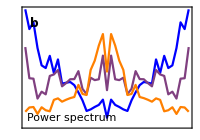

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

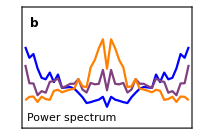

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.02,0.14},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[-1,1,0.02]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.75,0.8}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.2cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+7*heightEws+heightBif+7*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotKurt,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxKurt,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSkew,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSkew,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotAc2,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc2,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 6th row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 7th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 8th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

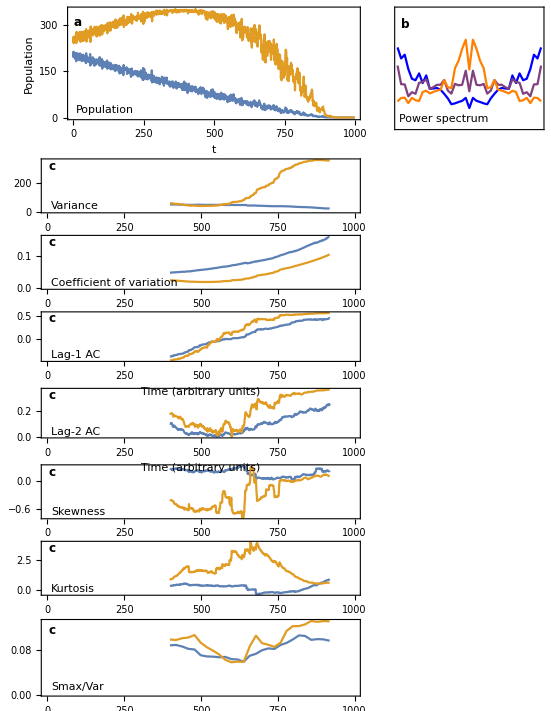

```mathematica
plotGrid
```

```mathematica
Export["figures/ews_trans_rnb_long.png",plotGrid,ImageResolution->200];
```